```mathematica
h[r1_,r2_]:=(r1+r2)Sin[ArcCos[(100-r1-r2)/(r1+r2)]]
```

```mathematica
Plot[h[50,r],{r,10,50}]
```

```mathematica
h[50,30]+h[30,49]
```

```mathematica
order=Range[50,30,-1]
```

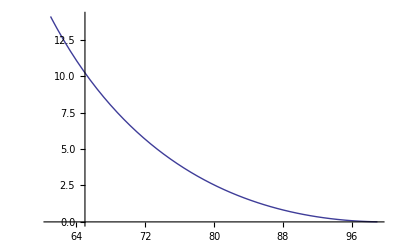

```mathematica
Plot[i-h[i/2,i/2],{i,61,99}]
```

```mathematica
order={49,47,45,43,41,39,37,35,33,31,30,32,34,36,38,40,42,44,46,48,50};
```

```mathematica
N[Total[h@@#&/@Table[order[[i;;i+1]],{i,1,Length[order]-1}]]+First[order]+Last[order],7]
```

1590.933